```mathematica
With[{T=1*^1,n=40000,Vr=10.,τ=20.*^-3,τrp=2.*^-3,dt=1.*^-4,CE=4000,JE=0.02,γ=1/4,g=4,α=1.2,θ=20.,νμ=#[[1]],νσ=#[[2]],να=#[[3]],νβ=#[[4]],cutoff=200},With[{νext=θ/(CE JE τ),CI=γ CE,JI=g JE,W=Sort@RandomVariate[NormalDistribution[],n],U=Sort@RandomVariate[StableDistribution[α,νβ,0,(1/2)^(1/α)],n],Uext=Sort@RandomVariate[StableDistribution[α,1,0,(1/2)^(1/α)],n]},With[{μdt=(CE νμ(1-g γ)+Sqrt[CE(1+g^2γ)]νσ W+(CE να)^(1/α)U+νext(CE+CE^(1/α)Uext))JE dt,σdt=(((CE JE^α+CI JI^α) νμ+CE JE^α νext) dt/2)^(1/α),β=((CE JE^α-CI JI^α) νμ+CE JE^α νext)/((CE JE^α+CI JI^α) νμ+CE JE^α νext)},Block[{V=ConstantArray[Vr,n],spikeNs=ConstantArray[0,n],i=1},For[,i dt≤T,i++,V+=-V dt/τ+μdt+σdt RandomVariate[StableDistribution[α,β,0,1],n];{spikeNs,V}=Through@{MapAt[#+1&,spikeNs,#]&,MapAt[Vr&,V,#]&}[Position[V,_?(GreaterEqualThan[θ])]];
If[Mod[i,100000]==0,Print[Through@{Mean,StandardDeviation,Moment[#,α]&,Histogram[#,List@Subdivide[0,200,30-1],"PDF"]&,Min,Max,Length,Mean@*Select[LessThan[cutoff]]@*Select[GreaterThan[-10]],StandardDeviation@*Select[LessThan[cutoff]]@*Select[GreaterThan[-10]],Moment[#,α]&@*Select[LessThan[cutoff]]@*Select[GreaterThan[-10]],Length@*Select[LessThan[cutoff]]@*Select[GreaterThan[-10]],Histogram[#,{"Log",50},"PDF"]&}[spikeNs/(spikeNs τrp+i dt)]]]]]]]]&@{47.091673291832294,33.55936083222739,96.5186128663704,-0.31221570654287367}
```

$Aborted

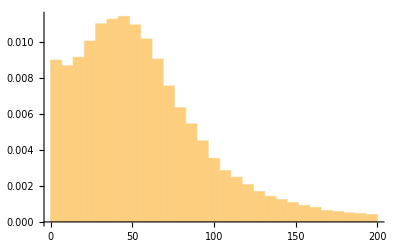
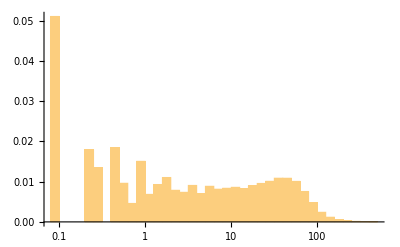
{64.2715,58.8044,159.634,-Graphics-,0.,476.188,40000,56.2285,39.1413,133.012,38607,-Graphics-}

```mathematica
With[{T=1*^1,n=40000,Vr=10.,τ=20.*^-3,τrp=2.*^-3,dt=1.*^-4,CE=4000,JE=0.02,γ=1/4,g=4,α=1.2,θ=20.,νμ=#[[1]],νσ=#[[2]],να=#[[3]],νβ=#[[4]],cutoff=200},With[{νext=θ/(CE JE τ),CI=γ CE,JI=g JE,W=Sort@RandomVariate[NormalDistribution[],n],U=Sort@RandomVariate[StableDistribution[α,νβ,0,(1/2)^(1/α)],n],Uext=Sort@RandomVariate[StableDistribution[α,1,0,(1/2)^(1/α)],n]},With[{μdt=(CE νμ(1-g γ)+Sqrt[CE(1+g^2γ)]νσ W+(CE να)^(1/α)U+νext(CE+CE^(1/α)Uext))JE dt,σdt=(((CE JE^α+CI JI^α) νμ+CE JE^α νext) dt/2)^(1/α),β=((CE JE^α-CI JI^α) νμ+CE JE^α νext)/((CE JE^α+CI JI^α) νμ+CE JE^α νext)},Block[{V=ConstantArray[Vr,n],spikeNs=ConstantArray[0,n],i=1},For[,i dt≤T,i++,V+=-V dt/τ+μdt+σdt RandomVariate[StableDistribution[α,β,0,1],n];{spikeNs,V}=Through@{MapAt[#+1&,spikeNs,#]&,MapAt[Vr&,V,#]&}[Position[V,_?(GreaterEqualThan[θ])]];
];Through@{Mean,StandardDeviation,Moment[#,α]&,Histogram[#,List@Subdivide[0,200,30-1],"PDF"]&,Min,Max,Length,Mean@*Select[LessThan[cutoff]]@*Select[GreaterThan[-10]],StandardDeviation@*Select[LessThan[cutoff]]@*Select[GreaterThan[-10]],Moment[#,α]&@*Select[LessThan[cutoff]]@*Select[GreaterThan[-10]],Length@*Select[LessThan[cutoff]]@*Select[GreaterThan[-10]],Histogram[#,{"Log",50},"PDF"]&}[spikeNs/(spikeNs τrp+i dt)]]]]]&@{47.091673291832294,33.55936083222739,96.5186128663704,-0.31221570654287367}
```

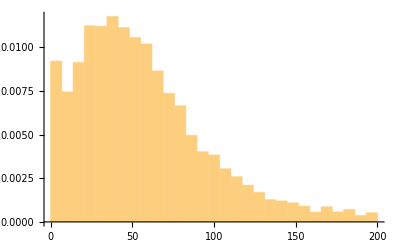
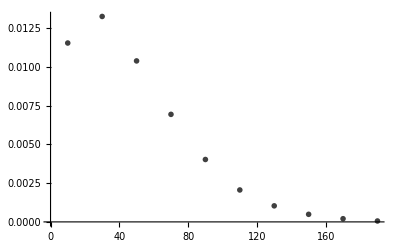
```mathematica
Show[-Graphics-,-Graphics-,Epilog->Inset[Show[-Graphics-,-Graphics-,-Graphics-,Frame->True,FrameTicksStyle->Directive[Black,8]],Scaled@{1,1},{Right,Top},125]]
```

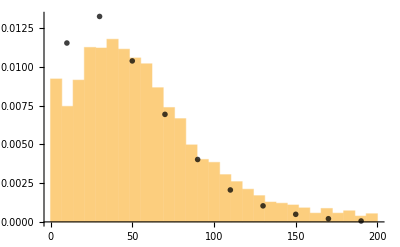

```mathematica
Last@(BinaryDeserialize@ByteArray[…])[[7]]
```

{103.69,76.4748,255.908,-0.306586}

```mathematica
ListLinePlot[Map[#[[1]]&]/@(BinaryDeserialize@ByteArray[…])[[{1,3,7,15,23,31,-1}]],PlotLabels->N@Range[105/100,2,5/200][[{1,3,7,15,23,31,-1}]]]
```

-Graphics-

```mathematica
ParallelTable[NestList[With[{T=1.*^0,n=20000,Vr=10.,τ=20.*^-3,τrp=2.*^-3,dt=1.*^-4,CE=4000,JE=0.02,γ=1/4,g=4,α=α,θ=20.,νμ=#[[1]],νσ=#[[2]],να=#[[3]],νβ=#[[4]]},With[{νext=θ/(CE JE τ),CI=γ CE,JI=g JE,W=Sort@RandomVariate[NormalDistribution[],n],U=Sort@RandomVariate[StableDistribution[α,νβ,0,(1/2)^(1/α)],n],Uext=Sort@RandomVariate[StableDistribution[α,1,0,(1/2)^(1/α)],n]},With[{μdt=(CE νμ(1-g γ)+Sqrt[CE(1+g^2γ)]νσ W+(CE να)^(1/α)U+νext(CE+CE^(1/α)Uext))JE dt,σdt=(((CE JE^α+CI JI^α) νμ+CE JE^α νext) dt/2)^(1/α),β=((CE JE^α-CI JI^α) νμ+CE JE^α νext)/((CE JE^α+CI JI^α) νμ+CE JE^α νext)},Block[{V=ConstantArray[Vr,n],spikeNs=ConstantArray[0,n],i=1},For[,i dt≤T,i++,V+=-V dt/τ+μdt+σdt RandomVariate[StableDistribution[α,β,0,1],n];{spikeNs,V}=Through@{MapAt[#+1&,spikeNs,#]&,MapAt[Vr&,V,#]&}[Position[V,_?(GreaterEqualThan[θ])]];
];Through@{Mean,StandardDeviation,Moment[Abs[#-g γ^(1/α)RandomSample[#]],α]&,With[{ν=#-g γ^(1/α)RandomSample[#]},Moment[Sign[ν]Abs[ν]^α,1]/Moment[Abs[ν],α]]&}[spikeNs/(spikeNs τrp+i dt)]]]]]&,{10.,10.,10.,0},30],{α,105/100,2,5/200}]//BinarySerialize
```

ByteArray[…]

```mathematica
ParallelTable[NestList[With[{T=1.*^0,n=40000,Vr=10.,τ=20.*^-3,τrp=2.*^-3,dt=1.*^-4,CE=4000,JE=0.02,γ=1/4,g=4,α=α,θ=20.,νμ=#[[1]],νσ=#[[2]],να=#[[3]],νβ=#[[4]]},With[{νext=θ/(CE JE τ),CI=γ CE,JI=g JE,W=RandomVariate[NormalDistribution[],n],U=RandomVariate[StableDistribution[α,νβ,0,(1/2)^(1/α)],n],Uext=RandomVariate[StableDistribution[α,1,0,(1/2)^(1/α)],n]},With[{μdt=(CE νμ(1-g γ)+Sqrt[CE(1+g^2γ)]νσ W+(CE να)^(1/α)U+νext(CE+CE^(1/α)Uext))JE dt,σdt=(((CE JE^α+CI JI^α) νμ+CE JE^α νext) dt/2)^(1/α),β=((CE JE^α-CI JI^α) νμ+CE JE^α νext)/((CE JE^α+CI JI^α) νμ+CE JE^α νext)},Block[{V=ConstantArray[Vr,n],spikeNs=ConstantArray[0,n],i=1},For[,i dt≤T,i++,V+=-V dt/τ+μdt+σdt RandomVariate[StableDistribution[α,β,0,1],n];{spikeNs,V}=Through@{MapAt[#+1&,spikeNs,#]&,MapAt[Vr&,V,#]&}[Position[V,_?(GreaterEqualThan[θ])]];
];Through@{Mean,StandardDeviation,Moment[Abs[#-g γ^(1/α)RandomSample[#]],α]&,With[{ν=#-g γ^(1/α)RandomSample[#]},Moment[Sign[ν]Abs[ν]^α,1]/Moment[Abs[ν],α]]&}[spikeNs/(spikeNs τrp+i dt)]]]]]&,{10.,10.,10.,0},30],{α,105/100,2,5/200}]//BinarySerialize
```

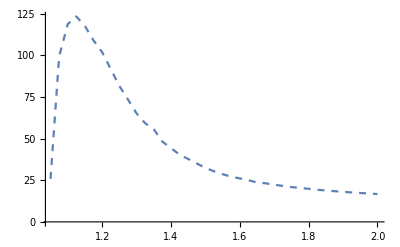

```mathematica
ListLinePlot[Range[105/100,2,5/200]~List~(First@*Last/@BinaryDeserialize@ByteArray[…])//Transpose,PlotStyle->Dashed]
```

```mathematica
ParallelTable[NestList[With[{T=1.*^0,n=1000,Vr=10.,τ=20.*^-3,τrp=2.*^-3,dt=1.*^-4,CE=4000,JE=0.02,γ=1/4,g=4,α=α,θ=20.,νμ=#[[1]],νσ=#[[2]],να=#[[3]],νβ=#[[4]]},If[νμ==0,Table[0,4],With[{νext=0.1θ/(CE JE τ),CI=γ CE,JI=g JE,W=Sort@RandomVariate[NormalDistribution[],n],U=Sort@RandomVariate[StableDistribution[α,νβ,0,(1/2)^(1/α)],n],Uext=Sort@RandomVariate[StableDistribution[α,1,0,(1/2)^(1/α)],n]},With[{μdt=(CE νμ(1-g γ)+Sqrt[CE(1+g^2γ)]νσ W+(CE να)^(1/α)U+νext(CE+CE^(1/α)Uext))JE dt,σdt=(((CE JE^α+CI JI^α) νμ+CE JE^α νext) dt/2)^(1/α),β=((CE JE^α-CI JI^α) νμ+CE JE^α νext)/((CE JE^α+CI JI^α) νμ+CE JE^α νext)},Block[{V=ConstantArray[Vr,n],spikeNs=ConstantArray[0,n],i=1},For[,i dt≤T,i++,V+=-V dt/τ+μdt+σdt RandomVariate[StableDistribution[α,β,0,1],n];{spikeNs,V}=Through@{MapAt[#+1&,spikeNs,#]&,MapAt[Vr&,V,#]&}[Position[V,_?(GreaterEqualThan[θ])]];
];Through@{Mean,StandardDeviation,Moment[Abs[#-g γ^(1/α)RandomSample[#]],α]&,With[{ν=#-g γ^(1/α)RandomSample[#]},Moment[Sign[ν]Abs[ν]^α,1]/(Moment[Abs[ν],α]/.{0.->∞})]&}[spikeNs/(spikeNs τrp+i dt)]]]]]]&,{10.,10.,10.,0},30],{α,Subdivide[1,2,20-1]}]//BinarySerialize
```

ByteArray[…]

```mathematica
ListLinePlot[Map[#[[1]]&]/@BinaryDeserialize[ResourceFunction["EvaluatePreviousCell"][]],PlotLabels->N@Subdivide[1,2,20-1]]
```

-Graphics-